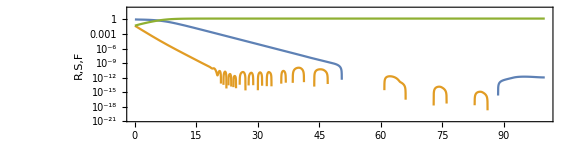

```mathematica
MetapopDyn[a_,λ_,σ_,ρ_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(X[t] + Y[t])*R[t] ,
X'[t] ==σ*(1-R[t])*Y[t] - ρ* R[t]*X[t] - μ*X[t],
Y'[t] ==λ*Y[t]*R[t]-σ*(1-R[t])*Y[t] +ρ* R[t] * X[t],
R[0]==1,X[0]==0.05,Y[0]==0.05},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=1,λ=0.5,σ=0,ρ=0.2,μ=1,T=100},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,λ,σ,ρ,μ,T] ];
LogPlot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","R,S,F"},ImageSize->Large]
]
```

The below code solves for the steady state

```mathematica
Sol =FullSimplify[Solve[{
0 == α*R*(1-R)-R*(X+Y),
0==σ*(1-R)*Y-ρ*R*X-μ*X,
0==λ*Y*R-σ*(1-R)*Y+ρ*R*X},
{R,X,Y}]]
```

{{R→0,X→0,Y→0},{R→1,X→0,Y→0},{R→-(μ (λ+σ)+√(μ (4 λ ρ σ+μ (λ+σ)^2)))/(2 λ ρ),X→1/(2 λ ρ (λ (μ+σ)+μ (-ρ+σ)))α (λ^2 (μ^2+2 ρ σ+μ (ρ+σ))+μ σ (μ σ+√(μ (λ^2 μ+2 λ (μ+2 ρ) σ+μ σ^2)))+λ (2 μ^2 σ+(ρ+σ) √(μ (λ^2 μ+2 λ (μ+2 ρ) σ+μ σ^2))+μ (3 ρ σ+σ^2+√(μ (λ^2 μ+2 λ (μ+2 ρ) σ+μ σ^2))))),Y→-(α (μ^2 (λ+σ)+λ μ (-λ+2 ρ+σ)+λ √(μ (4 λ ρ σ+μ (λ+σ)^2))+μ √(μ (4 λ ρ σ+μ (λ+σ)^2))))/(2 λ (λ (μ+σ)+μ (-ρ+σ)))},{R→(-μ (λ+σ)+√(μ (4 λ ρ σ+μ (λ+σ)^2)))/(2 λ ρ),X→1/(2 λ ρ (λ (μ+σ)+μ (-ρ+σ)))α (λ^2 (μ^2+2 ρ σ+μ (ρ+σ))+μ σ (μ σ-√(μ (λ^2 μ+2 λ (μ+2 ρ) σ+μ σ^2)))+λ (2 μ^2 σ-(ρ+σ) √(μ (λ^2 μ+2 λ (μ+2 ρ) σ+μ σ^2))+μ (3 ρ σ+σ^2-√(μ (λ^2 μ+2 λ (μ+2 ρ) σ+μ σ^2))))),Y→(α (λ μ (λ-2 ρ-σ)-μ^2 (λ+σ)+λ √(μ (4 λ ρ σ+μ (λ+σ)^2))+μ √(μ (4 λ ρ σ+μ (λ+σ)^2))))/(2 λ (λ (μ+σ)+μ (-ρ+σ)))}}

Define the single internal Fixed Point (and ensure that all variables are positive for positive parameter values)

```mathematica
InternalSol1 = Sol[[4]];
(*InternalSol2 = Sol[[4]];*)
{InternalSol1}/.{α->1,λ->0.1,μ->0.2,ρ->0.5,σ->0.5}
```

{{R→0.654724,X→0.0851541,Y→0.260122}}

INTERNAL, POSITIVE SOLUTION

```mathematica
IntPosSol = InternalSol1;
```

Define the internal Fixed Point solutions

```mathematica
Rstar = FullSimplify[IntPosSol[[1]][[2]]]
Sstar = FullSimplify[IntPosSol[[2]][[2]]]
Fstar = FullSimplify[IntPosSol[[3]][[2]]]
```

(-μ (λ+σ)+√(μ (4 λ ρ σ+μ (λ+σ)^2)))/(2 λ ρ)

1/(2 λ ρ (λ (μ+σ)+μ (-ρ+σ)))α (λ^2 (μ^2+2 ρ σ+μ (ρ+σ))+μ σ (μ σ-√(μ (λ^2 μ+2 λ (μ+2 ρ) σ+μ σ^2)))+λ (2 μ^2 σ-(ρ+σ) √(μ (λ^2 μ+2 λ (μ+2 ρ) σ+μ σ^2))+μ (3 ρ σ+σ^2-√(μ (λ^2 μ+2 λ (μ+2 ρ) σ+μ σ^2)))))

(α (λ μ (λ-2 ρ-σ)-μ^2 (λ+σ)+λ √(μ (4 λ ρ σ+μ (λ+σ)^2))+μ √(μ (4 λ ρ σ+μ (λ+σ)^2))))/(2 λ (λ (μ+σ)+μ (-ρ+σ)))

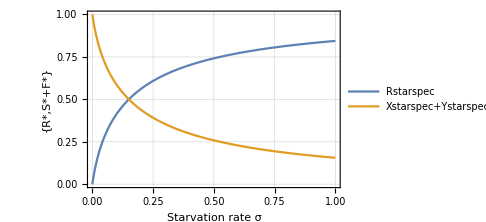
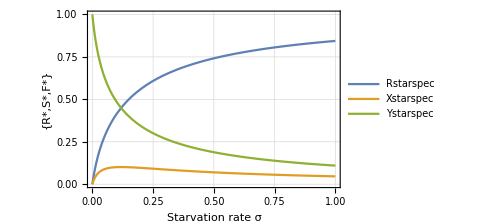

```mathematica
With[{alpha=1,lambda=0.1,mu=0.2,rho=0.2},
Rstarspec = IntPosSol[[1]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho};
Xstarspec = IntPosSol[[2]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho};
Ystarspec = IntPosSol[[3]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho};
Plot[{Rstarspec,Xstarspec,Ystarspec},{σ,0,1},PlotTheme->"Detailed",FrameLabel->{"Starvation rate σ","{R*,S*,F*}"},PlotRange->{{0,1},{0,1}},ImageSize->Medium]
Plot[{Rstarspec,Xstarspec+Ystarspec},{σ,0,1},PlotTheme->"Detailed",FrameLabel->{"Starvation rate σ","{R*,S*+F*}"},PlotRange->{0,All},ImageSize->Medium]
]
```

```mathematica
dR=   α*R*(1-R)-R*(S+F);
dS =σ*(1-R)*F-ρ*R*S-μ*S;
dF =λ*R*F-σ*(1-R)*F+ρ*R*S;
JacSpec = {
{D[dR,R],D[dR,S],D[dR,F]},
{D[dS,R],D[dS,S],D[dS,F]},
{D[dF,R],D[dF,S],D[dF,F]}
}
```

{{-F-S+(1-R) α-R α,-R,-R},{-S ρ-F σ,-μ-R ρ,(1-R) σ},{F λ+S ρ+F σ,R ρ,R λ-(1-R) σ}}

```mathematica
JacSpec//MatrixForm
```

(-F-S+(1-R) α-R α | -R | -R
-S ρ-F σ | -μ-R ρ | (1-R) σ
F λ+S ρ+F σ | R ρ | R λ-(1-R) σ)

```mathematica
JacSpecSol = JacSpec/.{R->Rstar,S->Sstar,F->Fstar};
```

Specific Bifurcations

```mathematica
Max[0,1]
```

1

This saddle node condtion is silly... the numerical solutions just imply that it exists at λ=0 and σ=0... the condition is not satisfied for parameter values > 0.

```mathematica
SaddleBifNum = Table[Flatten[{SIG,Select[λ/.NSolve[N[Det[JacSpecSol/.{α->1,μ->0.2,ρ->0.2,σ->SIG}]]==0,λ],Re[#]≥0.0001 && Im[#]==0&]}],{SIG,0,0.5,0.01}]
```

{{0.,0.200002},{0.01},{0.02},{0.03,0.147854,0.147798},{0.04,0.133323,0.133344},{0.05},{0.06,0.107676,0.107708},{0.07,0.0962841,0.0963085},{0.08,0.0856916,0.0857369},{0.09},{0.1,0.0666533,0.06668},{0.11},{0.12,0.0499847,0.0499949,0.0500051,0.0500153},{0.13,0.042442,0.0424065},{0.14,0.0352781,0.0352886,0.0352996,0.0353102},{0.15},{0.16},{0.17},{0.18,0.010526},{0.19},{0.2},{0.21},{0.22},{0.23},{0.24},{0.25},{0.26},{0.27},{0.28},{0.29},{0.3},{0.31},{0.32},{0.33},{0.34},{0.35},{0.36},{0.37},{0.38},{0.39},{0.4},{0.41},{0.42},{0.43},{0.44},{0.45},{0.46},{0.47},{0.48},{0.49},{0.5}}

```mathematica
Select[λ/.SaddleBifAnalytic[[1]],Re[#]>0 && Im[#]==0&]
```

{0.0666651}

```mathematica
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
```

```mathematica
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
```

```mathematica
HopfNum = Table[Flatten[{SIG,Quiet[Select[λ/.NSolve[N[Det[Sylv/.{α->0.5,μ->0.2,ρ->0.2,σ->SIG}]]==0,λ],Re[#]≥0.0001 && Im[#]==0&]]}],{SIG,0,1,0.1}]
```

{{0.,1.34512},{0.01,4.35171,0.180952,0.180952},{0.02,2.39605,0.163636,0.163636},{0.03,1.76662,0.147826,0.147826},{0.04,2.31291×10^14,1.46458,0.133333,0.133333},{0.05,1.29119,0.12,0.12},{0.06,1.18087,0.107692,0.107692},{0.07,1.10587,0.0962963,0.0962963},{0.08,1.05254,0.0857143,0.0857143},{0.09,1.0134,0.0758621,0.0758621},{0.1,0.984031,0.0666667,0.0666667},{0.11,0.961674,0.0580645,0.0580645},{0.12,0.944502,0.05,0.05},{0.13,0.931272,0.0424242,0.0424242},{0.14,0.921105,0.0352941,0.0352941},{0.15,0.913364,0.0285714,0.0285714},{0.16,0.907574,0.0222222,0.0222222},{0.17,0.903378,0.0162162,0.0162162},{0.18,0.900499,0.0105263,0.0105263},{0.19,0.89872,0.00512821,0.00512821},{0.2,0.89787},{0.21,0.89781},{0.22,0.898428},{0.23,0.899632},{0.24,0.901346},{0.25,0.903507},{0.26,0.90606},{0.27,0.908961},{0.28,0.912171},{0.29,0.915656},{0.3,0.919389},{0.31,0.923345},{0.32,0.927502},{0.33,0.931841},{0.34,0.936347},{0.35,0.941004},{0.36,0.945801},{0.37,0.950724},{0.38,0.955765},{0.39,0.960915},{0.4,0.966165},{0.41,0.971509},{0.42,0.976939},{0.43,0.98245},{0.44,0.988037},{0.45,0.993696},{0.46,0.99942},{0.47,1.00521},{0.48,1.01105},{0.49,1.01696},{0.5,1.02291},{0.51,1.02892},{0.52,1.03497},{0.53,1.04107},{0.54,1.04722},{0.55,1.0534},{0.56,1.05963},{0.57,1.06589},{0.58,1.07219},{0.59,1.07852},{0.6,1.08489},{0.61,1.09129},{0.62,1.09773},{0.63,1.10419},{0.64,1.11069},{0.65,1.11721},{0.66,1.12376},{0.67,1.13034},{0.68,1.13695},{0.69,1.14358},{0.7,5.10484×10^15,1.15024},{0.71,1.15692},{0.72,1.16362},{0.73,1.17036},{0.74,1.17711},{0.75,1.18389},{0.76,1.19069},{0.77,1.19751},{0.78,1.20435},{0.79,1.21122},{0.8,1.21811},{0.81,1.22502},{0.82,1.23195},{0.83,1.2389},{0.84,1.24587},{0.85,1.25286},{0.86,1.25987},{0.87,1.2669},{0.88,1.27395},{0.89,1.28102},{0.9,1.28811},{0.91,1.29522},{0.92,1.30234},{0.93,1.30949},{0.94,1.31666},{0.95,1.32384},{0.96,1.33104},{0.97,1.33826},{0.98,1.3455},{0.99,1.35276},{1.,1.36004}}

The Hopf bifurcaiton does exist... the bifurcation space shown below can be verified by playing with different simulations

```mathematica
points = Select[HopfNum,Length[#]==2&];
ifun = Interpolation[points]
```

InterpolatingFunction[{{0., 1.}}, <>]

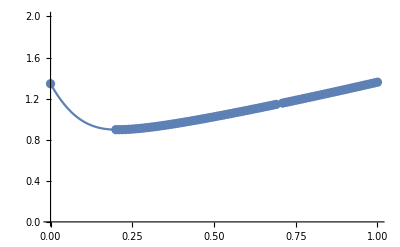

```mathematica
Show[{
ListPlot[Select[HopfNum,Length[#]==2&],PlotRange->{0,2}],
Plot[ifun[x],{x,0,1}]
}]
```

```mathematica
Interpoints = Table[{x,N[ifun[x]]},{x,0,1,.001}];
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/HopfDataFR.csv",Interpoints,"CSV"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/HopfDataFR.csv

```mathematica
Select[HopfNum,Length[#]==2&]
```

{{0.,1.34512},{0.2,0.89787},{0.25,0.903507},{0.3,0.919389},{0.35,0.941004},{0.4,0.966165},{0.45,0.993696},{0.5,1.02291},{0.55,1.0534},{0.6,1.08489},{0.65,1.11721},{0.75,1.18389},{0.8,1.21811},{0.85,1.25286},{0.9,1.28811},{0.95,1.32384},{1.,1.36004}}

Three-dimensional Hopf Bifurcaiton condition?

```mathematica
HopfNum3D = Table[Flatten[{SIG,ALPHA,Quiet[Select[λ/.NSolve[N[Det[Sylv/.{α->ALPHA,μ->0.2,ρ->0.2,σ->SIG}]]==0,λ],Re[#]≥0.0001 && Im[#]==0&]]}],{SIG,0,1,0.05},{ALPHA,0,1,0.1}]
```

{{{0.,0.},{0.,0.1,1.34512},{0.,0.2,1.34512},{0.,0.3,1.34512},{0.,0.4,1.34512},{0.,0.5,1.34512},{0.,0.6,1.34512},{0.,0.7,1.34512},{0.,0.8,1.34512},{0.,0.9,1.34512},{0.,1.,1.34512}},{{0.05,0.,0.1028,0.0529721,0.00330746},{0.05,0.1,0.900833,0.12,0.12},{0.05,0.2,0.99814,0.12,0.12},{0.05,0.3,1.09563,0.12,0.12},{0.05,0.4,1.19332,0.12,0.12},{0.05,0.5,1.29119,0.12,0.12},{0.05,0.6,1.38924,0.12,0.12},{0.05,0.7,1.48744,0.12,0.12},{0.05,0.8,1.58578,0.12,0.12},{0.05,0.9,1.68425,0.12,0.12},{0.05,1.,1.78284,0.12,0.12}},{{0.1,0.,0.16228,0.0448711},{0.1,0.1,0.636509,0.0666667,0.0666667},{0.1,0.2,0.721517,0.0666667,0.0666667},{0.1,0.3,0.80782,0.0666667,0.0666667},{0.1,0.4,0.895356,0.0666667,0.0666667},{0.1,0.5,0.984031,0.0666667,0.0666667},{0.1,0.6,1.07374,0.0666667,0.0666667},{0.1,0.7,1.16438,0.0666667,0.0666667},{0.1,0.8,1.25586,0.0666667,0.0666667},{0.1,0.9,1.34808,0.0666667,0.0666667},{0.1,1.,1.44097,0.0666667,0.0666667}},{{0.15,0.,0.0102207},{0.15,0.1,0.5859,0.0285714,0.0285714},{0.15,0.2,0.665895,0.0285714,0.0285714},{0.15,0.3,0.747114,0.0285714,0.0285714},{0.15,0.4,0.829609,0.0285714,0.0285714},{0.15,0.5,0.913364,0.0285714,0.0285714},{0.15,0.6,0.998326,0.0285714,0.0285714},{0.15,0.7,1.08442,0.0285714,0.0285714},{0.15,0.8,1.17157,0.0285714,0.0285714},{0.15,0.9,1.2597,0.0285714,0.0285714},{0.15,1.,1.34872,0.0285714,0.0285714}},{{0.2,0.},{0.2,0.1,0.578747},{0.2,0.2,0.657114},{0.2,0.3,0.736335},{0.2,0.4,0.816565},{0.2,0.5,0.89787},{0.2,0.6,0.980261},{0.2,0.7,1.06372},{0.2,0.8,1.14821},{0.2,0.9,1.23368},{0.2,1.,1.32007}},{{0.25,0.,0.224196,0.000686045},{0.25,0.1,0.586794},{0.25,0.2,0.665103},{0.25,0.3,0.743853},{0.25,0.4,0.823278},{0.25,0.5,0.903507},{0.25,0.6,0.984609},{0.25,0.7,1.06661},{0.25,0.8,1.14951},{0.25,0.9,1.2333},{0.25,1.,1.31795}},{{0.3,0.,0.328043,0.0333798},{0.3,0.1,0.601764},{0.3,0.2,0.680839},{0.3,0.3,0.759956},{0.3,0.4,0.839412},{0.3,0.5,0.919389},{0.3,0.6,1.},{0.3,0.7,1.08131},{0.3,0.8,1.16335},{0.3,0.9,1.24615},{0.3,1.,1.32968}},{{0.35,0.,3.52267,0.570383},{0.35,0.1,0.620446},{0.35,0.2,0.700761},{0.35,0.3,0.780747},{0.35,0.4,0.860752},{0.35,0.5,0.941004},{0.35,0.6,1.02165},{0.35,0.7,1.10279},{0.35,0.8,1.18449},{0.35,0.9,1.26678},{0.35,1.,1.34968}},{{0.4,0.,4.43779,0.00574224},{0.4,0.1,0.641363},{0.4,0.2,0.723215},{0.4,0.3,0.804389},{0.4,0.4,0.885284},{0.4,0.5,0.966165},{0.4,0.6,1.04721},{0.4,0.7,1.12855},{0.4,0.8,1.21027},{0.4,0.9,1.29243},{0.4,1.,1.37506}},{{0.45,0.,0.556683},{0.45,0.1,0.66376},{0.45,0.2,0.747341},{0.45,0.3,0.829918},{0.45,0.4,0.911936},{0.45,0.5,0.993696},{0.45,0.6,1.07541},{0.45,0.7,1.15722},{0.45,0.8,1.23923},{0.45,0.9,1.32153},{0.45,1.,1.40417}},{{0.5,0.,0.67455,0.0810807},{0.5,0.1,0.687218},{0.5,0.2,0.772658},{0.5,0.3,0.856788},{0.5,0.4,0.940095},{0.5,0.5,1.02291},{0.5,0.6,1.10548},{0.5,0.7,1.18796},{0.5,0.8,1.27048},{0.5,0.9,1.35314},{0.5,1.,1.43601}},{{0.55,0.,0.0884251},{0.55,0.1,0.711491},{0.55,0.2,0.798883},{0.55,0.3,0.884673},{0.55,0.4,0.969391},{0.55,0.5,1.0534},{0.55,0.6,1.13696},{0.55,0.7,1.22027},{0.55,0.8,1.30346},{0.55,0.9,1.38665},{0.55,1.,1.46991}},{{0.6,0.},{0.6,0.1,0.736431},{0.6,0.2,0.825841},{0.6,0.3,0.913369},{0.6,0.4,0.999587},{0.6,0.5,1.08489},{0.6,0.6,1.16956},{0.6,0.7,1.25382},{0.6,0.8,1.33781},{0.6,0.9,1.42165},{0.6,1.,1.50546}},{{0.65,0.},{0.65,0.1,0.761946},{0.65,0.2,0.85342},{0.65,0.3,0.942745},{0.65,0.4,1.03053},{0.65,0.5,1.11721},{0.65,0.6,1.20308},{0.65,0.7,1.28837},{0.65,0.8,1.37326},{0.65,0.9,1.45788},{0.65,1.,1.54233}},{{0.7,0.,0.00541473},{0.7,0.1,0.787977},{0.7,0.2,0.88155},{0.7,0.3,0.972716},{0.7,0.4,1.06213},{0.7,0.5,5.10484×10^15,1.15024},{0.7,0.6,1.23737},{0.7,0.7,1.32378},{0.7,0.8,1.40965},{0.7,0.9,1.49512},{0.7,1.,1.58032}},{{0.75,0.},{0.75,0.1,0.814489},{0.75,0.2,0.910186},{0.75,0.3,1.00322},{0.75,0.4,1.0943},{0.75,0.5,1.18389},{0.75,0.6,1.27234},{0.75,0.7,1.35993},{0.75,0.8,1.44684},{0.75,0.9,1.53325},{0.75,1.,1.61927}},{{0.8,0.,0.0140108},{0.8,0.1,0.841458},{0.8,0.2,0.939296},{0.8,0.3,1.03423},{0.8,0.4,1.127},{0.8,0.5,1.21811},{0.8,0.6,1.30793},{0.8,0.7,1.39674},{0.8,0.8,1.48476},{0.8,0.9,1.57215},{0.8,1.,1.65905}},{{0.85,0.,0.287575},{0.85,0.1,0.868871},{0.85,0.2,0.968862},{0.85,0.3,1.06572},{0.85,0.4,1.1602},{0.85,0.5,1.25286},{0.85,0.6,1.34408},{0.85,0.7,1.43416},{0.85,0.8,1.52332},{0.85,0.9,1.61175},{0.85,1.,1.69959}},{{0.9,0.},{0.9,0.1,0.896722},{0.9,0.2,0.998873},{0.9,0.3,1.09766},{0.9,0.4,1.19388},{0.9,0.5,1.28811},{0.9,0.6,1.38076},{0.9,0.7,1.47213},{0.9,0.8,1.56248},{0.9,0.9,1.65199},{0.9,1.,1.74082}},{{0.95,0.},{0.95,0.1,0.925008},{0.95,0.2,1.02932},{0.95,0.3,1.13004},{0.95,0.4,1.22802},{0.95,0.5,1.32384},{0.95,0.6,1.41794},{0.95,0.7,1.51064},{0.95,0.8,1.60221},{0.95,0.9,1.69283},{0.95,1.,1.78267}},{{1.,0.,0.70744},{1.,0.1,0.95373},{1.,0.2,1.06021},{1.,0.3,1.16288},{1.,0.4,1.26261},{1.,0.5,1.36004},{1.,0.6,1.45561},{1.,0.7,1.54966},{1.,0.8,1.64246},{1.,0.9,1.73423},{1.,1.,1.82512}}}

```mathematica
ListPlot3D[Select[Flatten[HopfNum3D,1],Length[#]==3&],AxesLabel->{"σ","α","λ"},PlotStyle->{Directive[ColorData[97,1],Opacity[0.8]],Directive[ColorData[97,2],Opacity[0.8]]},Lighting->{{"Ambient", White}}]
```

-Graphics3D-